```mathematica
Integrate[Sin[θE],{θE,0,π}]
```

2

```mathematica
ArcCos[1]
ArcCos[-1]
```

0

π

```mathematica
Integrate[1,{cosθE,-1,1}]
```

2

(2 Sinh[A sinθv])/(A sinθv)

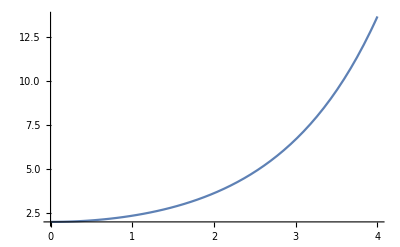

```mathematica
Integrate[E^(-A (sinθv cosθE(*+cosθv √(1-cosθE^2)*))),{cosθE,-1,1}]
Plot[%/.A -> x/sinθv,{x,0,4}]
```

π (-BesselI[1,A cosθv]+StruveL[-1,A cosθv])

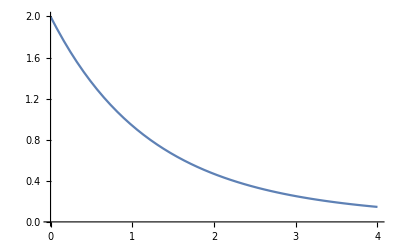

```mathematica
Integrate[Sin[θE] E^(-A (cosθv  Sin[θE])),{θE,0,π}]
Plot[%/.A -> x/cosθv,{x,0,4}]
```